```mathematica
Clear[g,χ,ξ1]

(* Gaussian sensing: Kitaev chain*)
QT[N1_]:=Module[{i,j,Matrix},
Matrix=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
Matrix[[i,i]]=1;
Matrix[[i,N1+i]]=1;
Matrix[[i+N1,i]]=-ⅈ;
Matrix[[i+N1,N1+i]]=ⅈ;
];
Matrix/√2
]

AMatrix[N1_,g_,ϕb_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i!=j && Abs[i-j]==1,
If[i<j,A[[i,j]]=g*Exp[-ⅈ*ϕb],
A[[i,j]]=-g*Exp[ⅈ*ϕb]
];
];
]
];
A
]

BMatrix[N1_,g_,ϕb_,χ_,ϕχ_, m_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[ Abs[i-j]==1,
If[i<j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
If[i>j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
];
];
];
A
]


BosonicKitaevChain[N1_,g_,ϕb_,χ_,ϕχ_,m_]:=Module[{},
A=AMatrix[N1,g,ϕb];
B=BMatrix[N1,g,ϕb,χ,ϕχ, m];
m1=Join[A,B,2];
m2=Join[Conjugate[B],Conjugate[A],2];
assump=g>=0&&χ>=0&&ϕb∈Reals&&ϕχ∈Reals;
$Assumptions=assump;
Simplify[Join[m1,m2]]
]

QFI[V_,mean_]:=Module[{},
4*Sum[mean[[2j-1]]*mean[[2j+1]]*V[[2j-1,2j+1]],{j,1,Length[V]/2-1}]
+ 4Sum[mean[[2j]]*mean[[2j+2]]*V[[2j,2j+2]],{j,1,Length[V]/2-1}]
+ 8Sum[mean[[2j-1]]*mean[[2j+2]]*V[[2j-1,2j+2]],{j,1,Length[V]/2-1}]
+8 Sum[mean[[2j]]*mean[[2j+1]]*V[[2j,2j+1]],{j,1,Length[V]/2-1}]
+4*Sum[ mean[[j]]mean[[j]]*V[[j,j]],{j,1,Length[V]}]
+2*Sum[V[[2j-1,2j+1]]^2,{j,1,Length[V]/2-1}]
+2*Sum[V[[2j,2j+2]]^2,{j,1,Length[V]/2-1}]
+4*Sum[V[[2j-1,2j+2]]^2,{j,1,Length[V]/2-1}]
]

CovarBasis[N1_]:= Module[{i,j,A},
A=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
A[[2i-1,i]]=1;
A[[2i,N1+i]]=1
];
A]



(* Gaussian sensing: Kitaev chain*)
AMatrix[N1_,g_,ϕb_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i!=j && Abs[i-j]==1,
If[i<j,A[[i,j]]=g*Exp[-ⅈ*ϕb],
A[[i,j]]=-g*Exp[ⅈ*ϕb]
];
];
]
];
A
]

BMatrix[N1_,g_,ϕb_,χ_,ϕχ_, m_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[ Abs[i-j]==1,
If[i<j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
If[i>j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
];
];
];
A
]


BosonicKitaevChain[N1_,g_,ϕb_,χ_,ϕχ_,m_]:=Module[{},
A=AMatrix[N1,g,ϕb];
B=BMatrix[N1,g,ϕb,χ,ϕχ, m];
m1=Join[A,B,2];
m2=Join[Conjugate[B],Conjugate[A],2];
assump=g>=0&&χ>=0&&ϕb∈Reals&&ϕχ∈Reals;
$Assumptions=assump;
Simplify[Join[m1,m2]]
]

QFI[V_,mean_]:=Module[{},
4*Sum[mean[[2j-1]]*mean[[2j+1]]*V[[2j-1,2j+1]],{j,1,Length[V]/2-1}]
+ 4Sum[mean[[2j]]*mean[[2j+2]]*V[[2j,2j+2]],{j,1,Length[V]/2-1}]
+ 8Sum[mean[[2j-1]]*mean[[2j+2]]*V[[2j-1,2j+2]],{j,1,Length[V]/2-1}]
+8 Sum[mean[[2j]]*mean[[2j+1]]*V[[2j,2j+1]],{j,1,Length[V]/2-1}]
+4*Sum[ mean[[j]]mean[[j]]*V[[j,j]],{j,1,Length[V]}]
+2*Sum[V[[2j-1,2j+1]]^2,{j,1,Length[V]/2-1}]
+2*Sum[V[[2j,2j+2]]^2,{j,1,Length[V]/2-1}]
+4*Sum[V[[2j-1,2j+2]]^2,{j,1,Length[V]/2-1}]
]

CovarBasis[N1_]:= Module[{i,j,A},
A=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
A[[2i-1,i]]=1;
A[[2i,N1+i]]=1
];
A]
CovarianceMatrix[S_,N1_]:=S.IdentityMatrix[2*N1].Transpose[S];
```

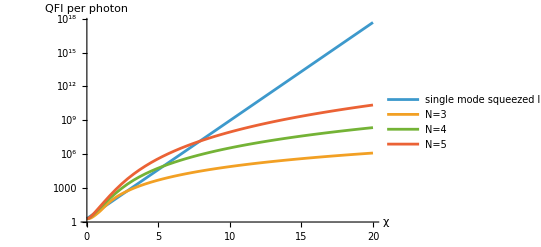

```mathematica
Clear[g,x];
PhotonNumbers[Cov_,Mean1_]:=Module[{},
1/2(Tr[Cov]-2*Nmodes)+ 1/2*Mean1.Mean1
];

Quads[Num_]:=Table[{Subscript[x, i],Subscript[p, i]},{i,1,Num}]//Flatten;
QuadsInit[Num_]:=Table[{Subscript[x, i]->x,Subscript[p, i]->0},{i,1,Num}]//Flatten;


QFIperPhoton[cov_,TransMatrix_,Nmodes_]:=Module[{vec,ph,res},
vec = TransMatrix.(Quads[Nmodes]/.QuadsInit[Nmodes]);
res=QFI[cov/4,vec] ;
ph=PhotonNumbers[cov,vec];
res/ph
]

(* Bosonic Kitaev Chain*)
Nmodes=4;
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM3=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]]/.{g->χ}//FullSimplify;
TransformMatrix= MatrixExp[DM3];
C1=CovarBasis[Nmodes];
BosonicKitaevTrans =C1.TransformMatrix.C1 //Simplify;
BosonicKitaevCov=CovarianceMatrix[BosonicKitaevTrans,Nmodes]//FullSimplify;

(* Single mode squeezing*)
SMDM=MatrixExp[{{χ,0},{0,-χ}}];
C1 = CovarBasis[1];
SMTransMatrix  =C1.SMDM.C1 //Simplify;
CovSMS=CovarianceMatrix[SMTransMatrix,1]//FullSimplify;


Clear[x]
Nmodes=6;
KitaevQFIperPhoton[Nmodes_]:=Module[{},
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM3=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]]/.{g->χ};
TransformMatrix= MatrixExp[DM3];
C1=CovarBasis[Nmodes];
BosonicKitaevTrans =C1.TransformMatrix.C1 ;
BosonicKitaevCov=CovarianceMatrix[BosonicKitaevTrans,Nmodes];
ResKitaev=QFI[BosonicKitaevCov/4,BosonicKitaevTrans.(Quads[Nmodes]/.QuadsInit[Nmodes])];
kitaevAmp=Coefficient[ResKitaev,x,2];
kitaevph= Coefficient[PhotonNumbers[BosonicKitaevCov,BosonicKitaevTrans.(Quads[Nmodes]/.QuadsInit[Nmodes])],x,2];
kitaevAmp/kitaevph
]



ResSqueezing=QFI[CovSMS/4,SMDM.(Quads[1]/.QuadsInit[1])];
squeezingAmp=Coefficient[ResSqueezing,x,2];
squeezingph =Coefficient[PhotonNumbers[CovSMS,SMDM.(Quads[1]/.QuadsInit[1])],x,2];

LogPlot[{squeezingAmp/squeezingph,KitaevQFIperPhoton[3],KitaevQFIperPhoton[4],KitaevQFIperPhoton[5]},{χ,0,20},AxesLabel->{"χ","QFI per photon"},PlotLegends->{"single mode squeezed light","N=3","N=4","N=5"}]
```

```mathematica
squeezingAmp/squeezingph
squeezingph
```

2 ⅇ^(2 χ)

ⅇ^(2 χ)/2

```mathematica
QFI[{{Cosh[2 χ],0,Sinh[2 χ],0},{0,Cosh[2 χ],0,-2 Cosh[χ] Sinh[χ]},{Sinh[2 χ],0,Cosh[2 χ],0},{0,-2 Cosh[χ] Sinh[χ],0,Cosh[2 χ]}},{x1,p1,x2,p2}]//FullSimplify
```

4 (p1^2+p2^2+x1^2+x2^2) Cosh[2 χ]+4 Sinh[2 χ] (-p1 p2+x1 x2+Sinh[2 χ])

```mathematica
Nmodes=4;
EOM=BosonicKitaevChain[Nmodes,g=0,ϕb=0,χ,ϕχ=0,{}]
DM3=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]]

"symplectic"
TransformMatrix= MatrixExp[DM3]//FullSimplify
C1=CovarBasis[Nmodes];
BosonicKitaevTrans =C1.TransformMatrix.C1 ;


"covariance matrix"
BosonicKitaevCov=CovarianceMatrix[BosonicKitaevTrans,Nmodes]//FullSimplify
ResKitaev=QFI[BosonicKitaevCov/4,{x1,p1,x2,p2}]//FullSimplify
ResKitaev=QFI[BosonicKitaevCov/4,{x1,p1,x2,p2}]//FullSimplify
```

{{0,0,0,0,0,χ,0,0},{0,0,0,0,χ,0,χ,0},{0,0,0,0,0,χ,0,χ},{0,0,0,0,0,0,χ,0},{0,χ,0,0,0,0,0,0},{χ,0,χ,0,0,0,0,0},{0,χ,0,χ,0,0,0,0},{0,0,χ,0,0,0,0,0}}

{{0,χ,0,0,0,0,0,0},{χ,0,χ,0,0,0,0,0},{0,χ,0,χ,0,0,0,0},{0,0,χ,0,0,0,0,0},{0,0,0,0,0,-χ,0,0},{0,0,0,0,-χ,0,-χ,0},{0,0,0,0,0,-χ,0,-χ},{0,0,0,0,0,0,-χ,0}}

symplectic

{{Cosh[χ/2] Cosh[(√5 χ)/2]-(Sinh[χ/2] Sinh[(√5 χ)/2])/(√5),(2 Cosh[χ/2] Sinh[(√5 χ)/2])/(√5),(2 Sinh[χ/2] Sinh[(√5 χ)/2])/(√5),Cosh[(√5 χ)/2] Sinh[χ/2]-(Cosh[χ/2] Sinh[(√5 χ)/2])/(√5),0,0,0,0},{(2 Cosh[χ/2] Sinh[(√5 χ)/2])/(√5),Cosh[χ/2] Cosh[(√5 χ)/2]+(Sinh[χ/2] Sinh[(√5 χ)/2])/(√5),Cosh[(√5 χ)/2] Sinh[χ/2]+(Cosh[χ/2] Sinh[(√5 χ)/2])/(√5),(2 Sinh[χ/2] Sinh[(√5 χ)/2])/(√5),0,0,0,0},{(2 Sinh[χ/2] Sinh[(√5 χ)/2])/(√5),Cosh[(√5 χ)/2] Sinh[χ/2]+(Cosh[χ/2] Sinh[(√5 χ)/2])/(√5),Cosh[χ/2] Cosh[(√5 χ)/2]+(Sinh[χ/2] Sinh[(√5 χ)/2])/(√5),(2 Cosh[χ/2] Sinh[(√5 χ)/2])/(√5),0,0,0,0},{Cosh[(√5 χ)/2] Sinh[χ/2]-(Cosh[χ/2] Sinh[(√5 χ)/2])/(√5),(2 Sinh[χ/2] Sinh[(√5 χ)/2])/(√5),(2 Cosh[χ/2] Sinh[(√5 χ)/2])/(√5),Cosh[χ/2] Cosh[(√5 χ)/2]-(Sinh[χ/2] Sinh[(√5 χ)/2])/(√5),0,0,0,0},{0,0,0,0,Cosh[χ/2] Cosh[(√5 χ)/2]-(Sinh[χ/2] Sinh[(√5 χ)/2])/(√5),-(2 Cosh[χ/2] Sinh[(√5 χ)/2])/(√5),(2 Sinh[χ/2] Sinh[(√5 χ)/2])/(√5),-Cosh[(√5 χ)/2] Sinh[χ/2]+(Cosh[χ/2] Sinh[(√5 χ)/2])/(√5)},{0,0,0,0,-(2 Cosh[χ/2] Sinh[(√5 χ)/2])/(√5),Cosh[χ/2] Cosh[(√5 χ)/2]+(Sinh[χ/2] Sinh[(√5 χ)/2])/(√5),-Cosh[(√5 χ)/2] Sinh[χ/2]-(Cosh[χ/2] Sinh[(√5 χ)/2])/(√5),(2 Sinh[χ/2] Sinh[(√5 χ)/2])/(√5)},{0,0,0,0,(2 Sinh[χ/2] Sinh[(√5 χ)/2])/(√5),-Cosh[(√5 χ)/2] Sinh[χ/2]-(Cosh[χ/2] Sinh[(√5 χ)/2])/(√5),Cosh[χ/2] Cosh[(√5 χ)/2]+(Sinh[χ/2] Sinh[(√5 χ)/2])/(√5),-(2 Cosh[χ/2] Sinh[(√5 χ)/2])/(√5)},{0,0,0,0,-Cosh[(√5 χ)/2] Sinh[χ/2]+(Cosh[χ/2] Sinh[(√5 χ)/2])/(√5),(2 Sinh[χ/2] Sinh[(√5 χ)/2])/(√5),-(2 Cosh[χ/2] Sinh[(√5 χ)/2])/(√5),Cosh[χ/2] Cosh[(√5 χ)/2]-(Sinh[χ/2] Sinh[(√5 χ)/2])/(√5)}}

covariance matrix

{{Cosh[χ] Cosh[√5 χ]-(Sinh[χ] Sinh[√5 χ])/(√5),0,(2 Cosh[χ] Sinh[√5 χ])/(√5),0,(2 Sinh[χ] Sinh[√5 χ])/(√5),0,Cosh[√5 χ] Sinh[χ]-(Cosh[χ] Sinh[√5 χ])/(√5),0},{0,Cosh[χ] Cosh[√5 χ]-(Sinh[χ] Sinh[√5 χ])/(√5),0,-(2 Cosh[χ] Sinh[√5 χ])/(√5),0,(2 Sinh[χ] Sinh[√5 χ])/(√5),0,-Cosh[√5 χ] Sinh[χ]+(Cosh[χ] Sinh[√5 χ])/(√5)},{(2 Cosh[χ] Sinh[√5 χ])/(√5),0,Cosh[χ] Cosh[√5 χ]+(Sinh[χ] Sinh[√5 χ])/(√5),0,Cosh[√5 χ] Sinh[χ]+(Cosh[χ] Sinh[√5 χ])/(√5),0,(2 Sinh[χ] Sinh[√5 χ])/(√5),0},{0,-(2 Cosh[χ] Sinh[√5 χ])/(√5),0,Cosh[χ] Cosh[√5 χ]+(Sinh[χ] Sinh[√5 χ])/(√5),0,-Cosh[√5 χ] Sinh[χ]-(Cosh[χ] Sinh[√5 χ])/(√5),0,(2 Sinh[χ] Sinh[√5 χ])/(√5)},{(2 Sinh[χ] Sinh[√5 χ])/(√5),0,Cosh[√5 χ] Sinh[χ]+(Cosh[χ] Sinh[√5 χ])/(√5),0,Cosh[χ] Cosh[√5 χ]+(Sinh[χ] Sinh[√5 χ])/(√5),0,(2 Cosh[χ] Sinh[√5 χ])/(√5),0},{0,(2 Sinh[χ] Sinh[√5 χ])/(√5),0,-Cosh[√5 χ] Sinh[χ]-(Cosh[χ] Sinh[√5 χ])/(√5),0,Cosh[χ] Cosh[√5 χ]+(Sinh[χ] Sinh[√5 χ])/(√5),0,-(2 Cosh[χ] Sinh[√5 χ])/(√5)},{Cosh[√5 χ] Sinh[χ]-(Cosh[χ] Sinh[√5 χ])/(√5),0,(2 Sinh[χ] Sinh[√5 χ])/(√5),0,(2 Cosh[χ] Sinh[√5 χ])/(√5),0,Cosh[χ] Cosh[√5 χ]-(Sinh[χ] Sinh[√5 χ])/(√5),0},{0,-Cosh[√5 χ] Sinh[χ]+(Cosh[χ] Sinh[√5 χ])/(√5),0,(2 Sinh[χ] Sinh[√5 χ])/(√5),0,-(2 Cosh[χ] Sinh[√5 χ])/(√5),0,Cosh[χ] Cosh[√5 χ]-(Sinh[χ] Sinh[√5 χ])/(√5)}}

Part::partw: Part 5 of {x1,p1,x2,p2} does not exist.

Part::partw: Part 7 of {x1,p1,x2,p2} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted

Part::partw: Part 5 of {x1,p1,x2,p2} does not exist.

Part::partw: Part 7 of {x1,p1,x2,p2} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(p1^2+p2^2+x1^2+x2^2) Cosh[2 χ]+Cosh[χ] Sinh[χ] (-2 p1 p2+2 x1 x2+Cosh[χ] Sinh[χ])/.{x1->0,x2->0,p1->0,p2->0}//FullSimplify
```

Cosh[χ]^2 Sinh[χ]^2

```mathematica
Σout=1/2 {{Cosh[2 r]-Cos[2 θ+ϕ] Sinh[2 r], Sin[2 θ+ϕ] Sinh[2 r]},{Sin[2 θ+ϕ] Sinh[2 r],Cosh[2 r]+Cos[2 θ+ϕ] Sinh[2 r]}};
λ=Sqrt[2] α {Cos[τ-θ],Sin[τ-θ]};

QFI[Σout,λ]//FullSimplify
```

4 α^2 (Cosh[2 r]-Cos[2 θ-2 τ] Cos[2 θ+ϕ] Sinh[2 r])